## Reference implementation for calculating points on the collision contour (manifold), for the exponential decay model

### General definitions

#### Dispersion relation

```mathematica
(* shift such that ω[1/2,η] = 2 *)
ω[k_,η_]:=2+1/2 (Tanh[η/2]-Sinh[η]/(Cosh[η]-Cos[2 k π]))
```

```mathematica
(* check *)
FullSimplify[1/2(5+Tanh[η/2])-Sum[Exp[-η j]Cos[2π j k],{j,0,∞}]-ω[k,η]]
```

0

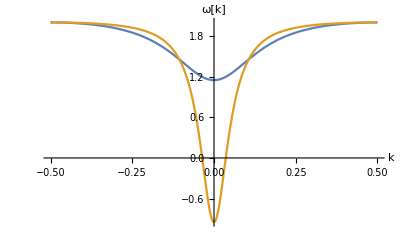

```mathematica
Plot[{ω[k,1],ω[k,1/3]},{k,-1/2,1/2},AxesLabel->{"k","ω[k]"},PlotRange->All]
```

#### Factorization of the energy difference

```mathematica
(* reference implementation *)
EnergyDifference[k1_,k2_,k3_,k4_,η_]:=ω[k1,η]+ω[k2,η]-ω[k3,η]-ω[k4,η]
```

```mathematica
Econtour[s12_,Δ12_,Δ34_,η_]:=-Cos[π s12]^3-Cosh[η](Cos[2π Δ12]+Cos[2π Δ34])+Cos[π s12](1+Cosh[η]^2+Cos[2π Δ12]Cos[2π Δ34])
```

```mathematica
Etriv[Δ12_,Δ34_]:=4 Sin[π (Δ12+Δ34)]Sin[π(Δ12-Δ34)]
```

```mathematica
Edenom[s12_,Δ12_,Δ34_,η_]:=Sinh[η]/2/((Cosh[η]-Cos[π (s12-2 Δ12)])(Cosh[η]-Cos[π (s12+2 Δ12)])(Cosh[η]-Cos[π (s12-2 Δ34)])(Cosh[η]-Cos[π (s12+2 Δ34)]))
```

```mathematica
FullSimplify[Solve[{k3+k4==s34,1/2(k3-k4)==Δ34},{k3,k4}]]
```

{{k3→s34/2+Δ34,k4→1/2 (s34-2 Δ34)}}

```mathematica
(* check *)
FullSimplify[EnergyDifference[1/2 s12+Δ12,1/2 s12-Δ12,1/2 s12+Δ34,1/2 s12-Δ34,η]-Edenom[s12,Δ12,Δ34,η]Econtour[s12,Δ12,Δ34,η]Etriv[Δ12,Δ34]]
```

0

#### Derivative of the energy difference with respect to s_12

```mathematica
(* derivative of 'Econtour' with respect to Subscript[s, 12] *)
dEcontour[s12_,Δ12_,Δ34_,η_]:=-π Sin[π s12](1+Cosh[η]^2+Cos[2 π Δ12] Cos[2 π Δ34]-3 Cos[π s12]^2)
```

```mathematica
(* check *)
FullSimplify[D[Econtour[s12,Δ12,Δ34,η],s12]-dEcontour[s12,Δ12,Δ34,η]]
```

0

```mathematica
(* derivative of 'Edenom' with respect to Subscript[s, 12] *)
dEdenom[s12_,Δ12_,Δ34_,η_]:=-π(Sin[π(s12-2Δ12)]/(Cosh[η]-Cos[π(s12-2Δ12)])+Sin[π(s12+2Δ12)]/(Cosh[η]-Cos[π(s12+2Δ12)])+Sin[π(s12-2Δ34)]/(Cosh[η]-Cos[π(s12-2Δ34)])+Sin[π(s12+2Δ34)]/(Cosh[η]-Cos[π(s12+2Δ34)]))Edenom[s12,Δ12,Δ34,η]
```

```mathematica
(* check *)
FullSimplify[D[Edenom[s12,Δ12,Δ34,η],s12]-dEdenom[s12,Δ12,Δ34,η]]
```

0

```mathematica
(* derivative of energy difference with respect to Subscript[s, 12] (using product rule), except "trivial" factor *)
dEdiff[s12_,Δ12_,Δ34_,η_]:=dEdenom[s12,Δ12,Δ34,η]Econtour[s12,Δ12,Δ34,η]+Edenom[s12,Δ12,Δ34,η]dEcontour[s12,Δ12,Δ34,η]
```

```mathematica
(* check *)
FullSimplify[D[Edenom[s12,Δ12,Δ34,η]Econtour[s12,Δ12,Δ34,η],s12]-dEdiff[s12,Δ12,Δ34,η]]
```

0

#### Calculation of s_12

```mathematica
CalculateSum12[Δ12_,Δ34_,η_]:=Module[{b=1+Cosh[η]^2+Cos[2π Δ12]Cos[2π Δ34],c=Cosh[η](Cos[2π Δ12]+Cos[2π Δ34]),x},1/π ArcCos[x/.FindRoot[x^3-b x+c,{x,0}]]]
```

```mathematica
(* check *)
Block[{η=1/3},Norm[Table[Econtour[CalculateSum12[Δ12,Δ34,η],Δ12,Δ34,η],{Δ12,-1,1,1/8},{Δ34,-1,1,1/8}],∞]]
```

4.28141×10^-15

```mathematica
Block[{η=1/3,s12},ParametricPlot3D[{1/2 s12+Δ12,1/2 s12+Δ34,1/2 s12-Δ34}/.{s12->CalculateSum12[Δ12,Δ34,η]},{Δ12,-1/2,1/2},{Δ34,-1/2,1/2},PlotPoints->50,AxesLabel->{"k_1","k_3","k_4"},Lighting->"Classic"]]
```

-Graphics3D-

### Numerical examples

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* uniform grid *)
Subscript[Δ, list]=Block[{gridsize=128},Range[-1/2,1/2-1/gridsize,1/gridsize]];
```

```mathematica
(* mollification parameter *)
Subscript[ϵ, val]=1/2;
```

```mathematica
(* points on the contour *)
Subscript[pts, contour]=Block[{η=1/3,s12},Flatten[Outer[Mod[N[{1/2 s12+#1,1/2 s12-#1,1/2 s12+#2,1/2 s12-#2}/.{s12->CalculateSum12[#1,#2,η]}],1]&,Subscript[Δ, list],Subscript[Δ, list]],1]];
Dimensions[%]
```

{16384,4}

```mathematica
(* derivative of the energy difference with respect to Subscript[s, 12] *)
Subscript[dω, contour]=Block[{η=1/3,s12},Flatten[Outer[N[dEdiff[s12,#1,#2,η]Etriv[#1,#2]/.{s12->CalculateSum12[#1,#2,η]}]&,Subscript[Δ, list],Subscript[Δ, list]],1]];
Dimensions[%]
```

{16384}

```mathematica
(* sort points *)
Ordering[Subscript[pts, contour],Length[Subscript[pts, contour]],#1⟦1⟧<#2⟦1⟧∨(#1⟦1⟧==#2⟦1⟧∧#1⟦3⟧<#2⟦3⟧)&];
{Subscript[pts, contour]=Subscript[pts, contour]⟦%⟧,Subscript[dω, contour]=Subscript[dω, contour]⟦%⟧};
```

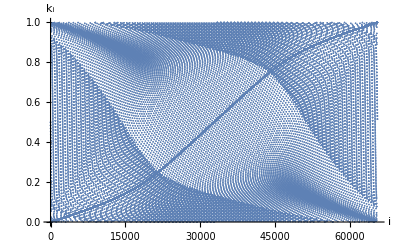

```mathematica
ListPlot[Flatten[Subscript[pts, contour]],AxesLabel->{"i","k_i"}]
```

```mathematica
Subscript[k, list]=Union[Flatten[Subscript[pts, contour]],SameTest->(Abs[#1-#2]<10^-12&)];
Dimensions[%]
```

{8320}

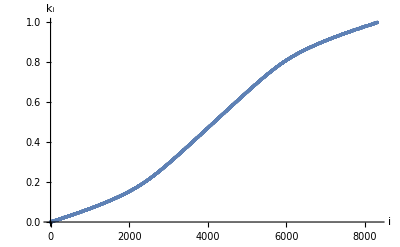

```mathematica
ListPlot[Subscript[k, list],AxesLabel->{"i","k_i"}]
```

```mathematica
(* mollified inverse of dω *)
Subscript[invdω, contour]=π(#^2+Subscript[ϵ, val]^2)^(-1/2)&/@Subscript[dω, contour];
Dimensions[%]
```

{16384}

```mathematica
(* save as reference to disk *)
Subscript[fn, base]="collision_contour_ref/exp";
Export[Subscript[fn, base]<>"_klist_ref.dat",Subscript[k, list],"Real64"];
Export[Subscript[fn, base]<>"_contour_k4_ref.dat",Flatten[Subscript[pts, contour]],"Real64"];
Export[Subscript[fn, base]<>"_idomega_ref.dat",Subscript[invdω, contour],"Real64"];
```